```mathematica
Clear[hbar, e0, m0, ηm];
hbar=6.58211899*10^(-16);  (* h/2π  in eV s *)
m0=9.10938215*10^(-31); 
e0=1.602176487*10^(-19);
ηm=hbar^2*e0*10^(20)/m0;  (* hbar^2/m0 in eV A^2 *)
μB=5.7883818066 * 10^(-2);    (* in meV/T *)
meVpK=8.6173325*10^(-2);   (* Kelvin into meV *)
(* **************************************** *)
```

```mathematica
Clear[ts, tsw, as, ms, Nx, Ny, Nxn, α, αw, Δ];
as=100.0; (* unit cell in A *)
ms=0.02;
ts=500*ηm/(2*as^2*ms); (* hopping in meV *)
α=200.0/as; (* Rashba coupling in meV *)
Δ=0.4; (* induced gap in meV *)
Nx=250;
NxM=10;
Nxn=0;
Ny=1;
asw=600.0/(Ny+1);
αw=α*as/asw;
tsw=4.0;
μ=0.0;
B=2Δ;

(*tϕ=ts/200;
αϕ=α/200;*)
tϕ1=0.4ts;
tϕ2=ts;
αϕ=0.0;
θ1=1.0π;
θM=0.5 π;
θ2=0.0;
```

```mathematica
a=SessionTime[];
IN={};
Imax={};
For[NxM=2,NxM≤100,NxM+=1,
eϕ={};
elϕ=Table[{},{n,1,10}];
For[ϕ=0,ϕ≤4π,ϕ+=0.1,

ϵ0=2ts Cos[Pi/(Nx+1.0)];
(*First Chain*)
H1σ11τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0+B Sin[θ1],Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H1σ22τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0-B Sin[θ1],Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H1σ12τ11=SparseArray[{Band[{1,1}]->B Cos[θ1],Band[{1,2}]->α/2,Band[{2,1}]->-α/2},{Nx,Nx}];
H1σ21τ11=SparseArray[{Band[{1,1}]->B Cos[θ1],Band[{1,2}]->-α/2,Band[{2,1}]->α/2},{Nx,Nx}];

H1σ12τ12=SparseArray[{Band[{1,1}]->Δ},{Nx,Nx}];
H1σ21τ12=SparseArray[{Band[{1,1}]->-Δ},{Nx,Nx}];

H1τ11=SparseArray[ArrayFlatten[{{H1σ11τ11,H1σ12τ11},{H1σ21τ11,H1σ22τ11}}]];
H1τ22=-H1τ11;
H1τ12=SparseArray[ArrayFlatten[{{0,H1σ12τ12},{H1σ21τ12,0}}]];
H1τ21=Conjugate[Transpose[H1τ12]];

H11=SparseArray[ArrayFlatten[{{H1τ11,H1τ12},{H1τ21,H1τ22}}]];


(*Middle Chain*)
HMσ11τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0+B Sin[θM],Band[{1,2}]->ts,Band[{2,1}]->ts},{NxM,NxM}];
HMσ22τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0-B Sin[θM],Band[{1,2}]->ts,Band[{2,1}]->ts},{NxM,NxM}];
HMσ12τ11=SparseArray[{Band[{1,1}]->B Cos[θM],Band[{1,2}]->α/2,Band[{2,1}]->-α/2},{NxM,NxM}];
HMσ21τ11=SparseArray[{Band[{1,1}]->B Cos[θM],Band[{1,2}]->-α/2,Band[{2,1}]->α/2},{NxM,NxM}];

HMσ12τ12=SparseArray[{Band[{1,1}]->Δ ⅇ^(ⅈ ϕ)},{NxM,NxM}];
HMσ21τ12=SparseArray[{Band[{1,1}]->-Δ ⅇ^(ⅈ ϕ)},{NxM,NxM}];

HMτ11=SparseArray[ArrayFlatten[{{HMσ11τ11,HMσ12τ11},{HMσ21τ11,HMσ22τ11}}]];
HMτ22=-HMτ11;
HMτ12=SparseArray[ArrayFlatten[{{0,HMσ12τ12},{HMσ21τ12,0}}]];
HMτ21=Conjugate[Transpose[HMτ12]];

HMM=SparseArray[ArrayFlatten[{{HMτ11,HMτ12},{HMτ21,HMτ22}}]];


(*Second Chain*)
H2σ11τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0+B Sin[θ2],Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H2σ22τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0-B Sin[θ2],Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H2σ12τ11=SparseArray[{Band[{1,1}]->B Cos[θ2],Band[{1,2}]->α/2,Band[{2,1}]->-α/2},{Nx,Nx}];
H2σ21τ11=SparseArray[{Band[{1,1}]->B Cos[θ2],Band[{1,2}]->-α/2,Band[{2,1}]->α/2},{Nx,Nx}];

H2σ12τ12=SparseArray[{Band[{1,1}]->Δ ⅇ^(ⅈ ϕ)},{Nx,Nx}];
H2σ21τ12=SparseArray[{Band[{1,1}]->-Δ ⅇ^(ⅈ ϕ)},{Nx,Nx}];

H2τ11=SparseArray[ArrayFlatten[{{H2σ11τ11,H2σ12τ11},{H2σ21τ11,H2σ22τ11}}]];
H2τ22=-H2τ11;
H2τ12=SparseArray[ArrayFlatten[{{0,H2σ12τ12},{H2σ21τ12,0}}]];
H2τ21=Conjugate[Transpose[H2τ12]];

H22=SparseArray[ArrayFlatten[{{H2τ11,H2τ12},{H2τ21,H2τ22}}]];

(*Tunnel Junction*)
H1M=SparseArray[{{Nx,1}->tϕ1,{2Nx,NxM+1}->tϕ1,{3Nx,2NxM+1}->-tϕ1,{4Nx,3NxM+1}->-tϕ1},{4Nx,4NxM}];
HM1=Conjugate[Transpose[H1M]];

HM2=SparseArray[{{NxM,1}->tϕ2,{2NxM,Nx+1}->tϕ2,{3NxM,2Nx+1}->-tϕ2,{4NxM,3Nx+1}->-tϕ2},{4NxM,4Nx}];
H2M=Conjugate[Transpose[HM2]];

(*Full Wire*)
Hsp=SparseArray[ArrayFlatten[{{H11,H1M,0},{HM1,HMM,HM2},{0,H2M,H22}}]];



etp=Sort[Eigenvalues[Hsp,-10]];
For[n=1,n≤Length[etp],n++,
elϕ[[n]]=Join[elϕ[[n]],{{ϕ,etp[[n]]}}]
];
If[π<ϕ<3π,
eϕ=Join[eϕ,{{ϕ,Sum[etp[[i]],{i,1,Length[etp]/2-2}]+etp[[Length[etp]/2+1]]+etp[[Length[etp]/2+2]]}}];
,
eϕ=Join[eϕ,{{ϕ,Sum[etp[[i]],{i,1,Length[etp]/2-2}]+etp[[Length[etp]/2-1]]+etp[[Length[etp]/2]]}}];
];


];

Iϕ={};
IϕM={};
For[ϕi=2,ϕi≤Length[eϕ],ϕi++,
Iϕ=Join[Iϕ,{{eϕ[[ϕi,1]],(eϕ[[ϕi,2]]-eϕ[[ϕi-1,2]])/(eϕ[[ϕi,1]]-eϕ[[ϕi-1,1]])}}];
IϕM=Join[IϕM,{Re[(eϕ[[ϕi,2]]-eϕ[[ϕi-1,2]])/(eϕ[[ϕi,1]]-eϕ[[ϕi-1,1]])]}];
];

IN=Join[IN,{IϕM}];
Imax=Join[Imax,{{NxM,Max[IϕM]}}];
Print[{NxM,Max[IϕM]}];
];
```

{2,0.00196112}

{3,0.00449942}

{4,0.00689974}

{5,0.0092312}

{6,0.0115552}

{7,0.0142859}

{8,0.0156614}

{9,0.0159542}

{10,0.0156103}

{11,0.0151831}

{12,0.0150169}

{13,0.0152571}

{14,0.0158537}

{15,0.0164969}

{16,0.0170485}

{17,0.0172675}

{18,0.0171052}

{19,0.0167378}

{20,0.0163836}

{21,0.0162071}

{22,0.0162552}

{23,0.016481}

{24,0.0168096}

{25,0.017161}

{26,0.0174272}

{27,0.0175442}

{28,0.0175214}

{29,0.0174225}

{30,0.0173234}

{31,0.0172796}

{32,0.0173117}

{33,0.0174075}

{34,0.0175333}

{35,0.017648}

{36,0.0177203}

{37,0.0177399}

{38,0.017717}

{39,0.0176762}

{40,0.0176426}

{41,0.0176326}

{42,0.0176508}

{43,0.0176891}

{44,0.0177341}

{45,0.0177716}

{46,0.0177929}

{47,0.0177961}

{48,0.0177865}

{49,0.0177729}

{50,0.0177632}

{51,0.0177625}

{52,0.0177705}

{53,0.0177846}

{54,4.05287}

{55,0.0178108}

{56,0.0178162}

{57,0.0178158}

{58,0.017812}

{59,0.0178074}

{60,0.0178048}

{61,0.0178054}

{62,0.0178088}

{63,0.0178138}

{64,0.0193143}

{65,0.0178222}

{66,0.0178231}

{67,0.0178227}

{68,0.017821}

{69,0.0178199}

{70,0.0178193}

{71,0.0178197}

{72,0.0178212}

{73,3.96941}

{74,0.943507}

{75,2.53229}

{76,0.0178256}

{77,0.0178251}

{78,0.0178247}

{79,0.0178242}

{80,0.017824}

{81,0.0178244}

{82,0.0178249}

{83,0.0323547}

{84,2.49801}

{85,3.97812}

{86,0.976286}

{87,0.0178261}

{88,0.0178259}

{89,0.0178258}

{90,0.0178258}

{91,3.98197}

{92,2.50593}

{93,2.53265}

{94,2.50668}

{95,0.0178268}

{96,2.53109}

{97,4.00861}

{98,2.49893}

{99,0.0499144}

{100,2.5308}

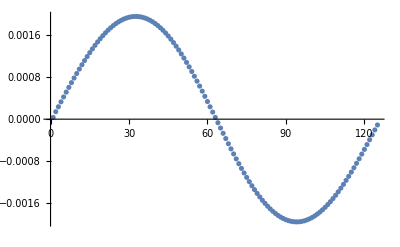

```mathematica
ListPlot[Re[IN[[1]]],PlotRange->All]
```

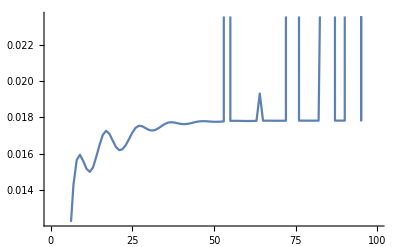

```mathematica
ListPlot[Imax,Joined->True]
```

```mathematica
(*Export["C:\\Users\\jsten\\Documents\\Reaserch\\Majorana spin\\Sparse Matrix\\Data\\Imax_NxM.mx",Imax]
Export["C:\\Users\\jsten\\Documents\\Reaserch\\Majorana spin\\Sparse Matrix\\Data\\I_NxM.mx",IN]*)
```

```mathematica
ImaxI=Import["C:\\Users\\jsten\\Documents\\Reaserch\\Majorana spin\\Sparse Matrix\\Data\\Imax_NxM.mx"];
INI=Import["C:\\Users\\jsten\\Documents\\Reaserch\\Majorana spin\\Sparse Matrix\\Data\\I_NxM.mx"];
```

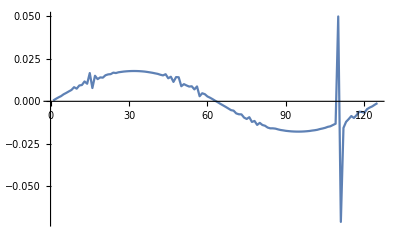

```mathematica
ListPlot[Re[IN[[98]]],PlotRange->All,Joined->True]
```

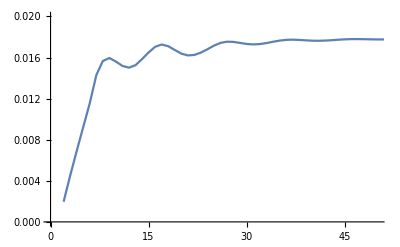

```mathematica
ListPlot[Imax,Joined->True,PlotRange->{{0,50},{0,0.02}}]
```